```mathematica
D[-Log[1-x^2], x]
Series[-Log[1-x^2], {x, 0, 2}]
D[1/Sqrt[1-x^2], x]
Series[1/Sqrt[1-x^2], {x,0,2}]
```

(2 x)/(1-x^2)

x^2+O[x]^3

x/((1-x^2)^(3/2))

1+x^2/2+O[x]^3

# Behavior of Cost Derivatives

## Near pairwise orthogonal

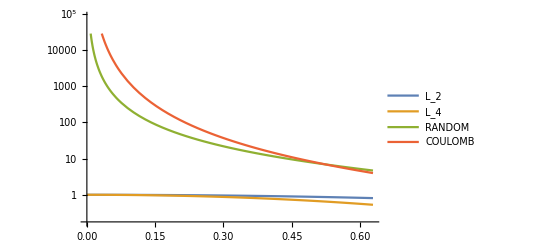

```mathematica
LogPlot[{Cos[x], Cos[x]^3, (2Cos[ x])/(1-Cos[x]^2), Cos[x]/((1-Cos[x]^2)^(3/2))}, {x, 0, Pi/5},PlotLegends->{"L_2", "L_4", "RANDOM", "COULOMB"}]
```

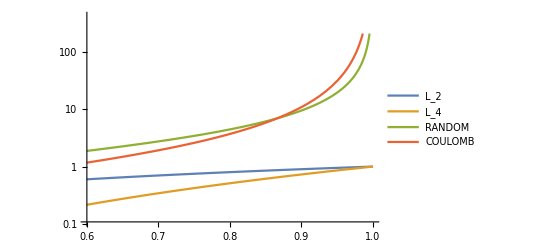

```mathematica
LogPlot[{x, x^3, (2 x)/(1-x^2), x/((1-x^2)^(3/2))}, {x, .6, 1},PlotLegends->{"L_2", "L_4", "RANDOM", "COULOMB"}]
```

## Near pairwise parallel

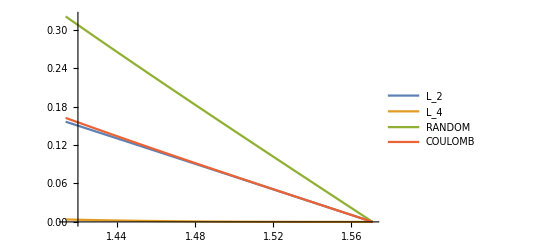

```mathematica
Plot[{Cos[x], Cos[x]^3, (2Cos[ x])/(1-Cos[x]^2), Cos[x]/((1-Cos[x]^2)^(3/2))}, {x, Pi/2-Pi/20, Pi/2},PlotLegends->{"L_2", "L_4", "RANDOM", "COULOMB"}]
```

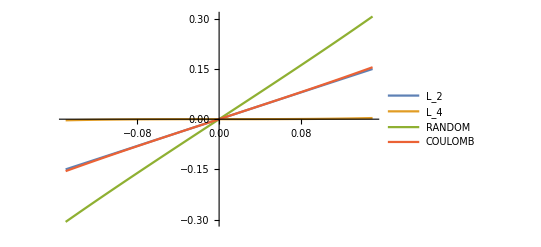

```mathematica
Plot[{x, x^3, (2 x)/(1-x^2), x/((1-x^2)^(3/2))}, {x, -.15, .15},PlotLegends->{"L_2", "L_4", "RANDOM", "COULOMB"}]
```

## Force on nearly orthogonal vs. other angles

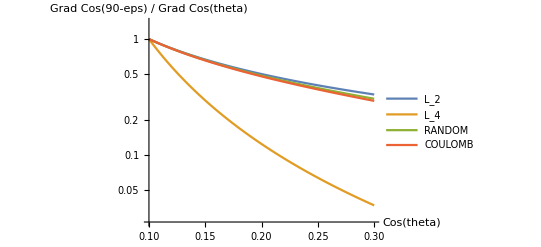

```mathematica
eps=.1;
end=.3;
LogPlot[{eps/x, eps^3/x^3, ((2 eps)/(1-eps^2))/((2 x)/(1-x^2)), (eps/((1-eps^2)^(3/2)))/(x/((1-x^2)^(3/2)))}, {x, eps, end},PlotLegends->{"L_2", "L_4", "RANDOM", "COULOMB"},AxesLabel->{"Cos(theta)", "Grad Cos(90-eps) / Grad Cos(theta)"}]
```

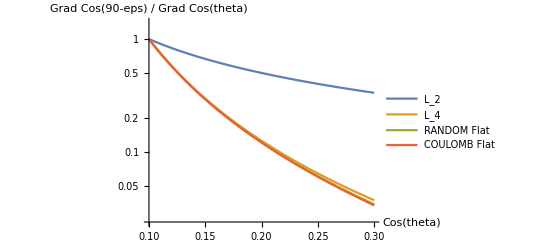

```mathematica
LogPlot[{eps/x, eps^3/x^3, ((2 eps)/(1-eps^2)-2eps)/(((2 x)/(1-x^2))-2x), (eps/((1-eps^2)^(3/2))-eps)/((x/((1-x^2)^(3/2)))-x)}, {x, eps, end},PlotLegends->{"L_2", "L_4", "RANDOM Flat", "COULOMB Flat"},AxesLabel->{"Cos(theta)", "Grad Cos(90-eps) / Grad Cos(theta)"}]
```

## Minimum possible coherence

128

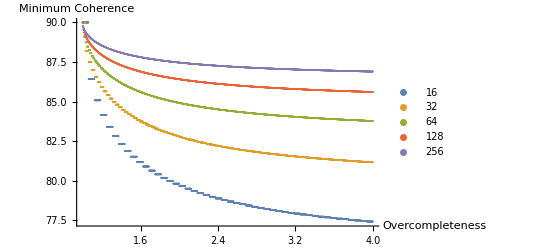

```mathematica
n = 128
ListPlot[Table[{oc, ArcCos[Sqrt[(IntegerPart[oc*2^sn]-2^sn)/(2^sn(IntegerPart[oc*2^sn]-1))]]*180/Pi}, {sn, 4, 8},{oc, 1, 4, .001}], PlotLegends->{16, 32, 64, 128, 256},AxesLabel->{"Overcompleteness", "Minimum Coherence"}]
```